# Projective Geometry

Desargues’ Theorem

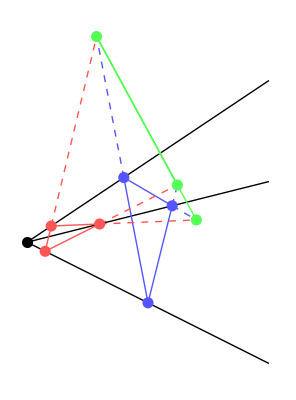

```mathematica
eqline[m1_,ra1_,m2_,ra2_]:=If[ra1>ra2,ra2 m2+(m1 ra1-m2 ra2)/(ra1 -ra2)(x-ra2),ra1 m1+(m2 ra2-m1 ra1)/(ra2 -ra1)(x-ra1)]
P0 = {0,0};

m1 = 2/3;
ra1 = 1;
rb1= 4;
m2 = 1/4;
ra2 = 3;
rb2 = 6;
m3 = -1/2;
ra3=3/4;
rb3 = 5;

a1 = ra1{1, m1};
b1 = rb1{1,m1};
a2 = ra2{1, m2};
b2 = rb2{1,m2};
a3 = ra3{1,m3};
b3 = rb3{1,m3};

a1a2 = eqline[m1,ra1,m2,ra2];
b1b2 = eqline[m1,rb1,m2,rb2];
a1a3 = eqline[m1,ra1,m3,ra3];
b1b3 = eqline[m1,rb1,m3,rb3];
a2a3 =eqline[m2,ra2,m3,ra3];
b2b3 =eqline[m2,rb2,m3,rb3];

x1 =Solve[a1a2==b1b2,x];
x2 =Solve[a1a3==b1b3,x];
x3 =Solve[a2a3==b2b3,x];

L1=Flatten@{Values@x1,a1a2/.x1};
L2=Flatten@{Values@x2,a1a3/.x2};
L3=Flatten@{Values@x3,a2a3/.x3};

Graphics[{
PointSize[.02],Point[{0,0}],
Line[{P0,10{1,m1}}],Line[{P0,10{1,m2}}],Line[{P0,10{1,m3}}],
Lighter@Red,Point[{a1,a2,a3}],
Line[{a1,a2,a3,a1}],
Lighter@Blue,Point[{b1,b2,b3}],
Line[{b1,b2,b3,b1}],
Dashed,
Lighter@Red, Line[{{a2,L1},{a1,L2},{a2,L3}}],
Lighter@Blue,Line[{{b2,L1},{b1,L2},{b2,L3}}],
Lighter@Green,Point[{L1,L2,L3}],Dashing[None],Line[{L1,L2,L3}]
}]
```